```mathematica
(*Helper functions for retrieving pieces of data from the mess put into them*)
notebookLocation=NotebookDirectory[];
select[list_,item_]:=If[(Select[list,MatchQ[#,item->_]&]=={}),item-> {"Not Listed"},Select[list,MatchQ[#,item->_]&]]
stringForm[object_]:= If[ListQ[object],object[[1]],object]
existsQ[list_,term_]:=!(Select[list,MatchQ[#,term]&]=={})
connect[lists_]:= ParallelTable[lists[[j,i]],{i,Length[lists[[1]]]},{j,Length[lists]}]

type[list_]:="Type"/.select[list,"Type"]
statusQ[list_]:= (type[list]=="status")&&existsQ[list,"Actions"->_]&&!existsQ[list,"Story"->_]

socialMediaQ[data_,term_]:=Select[data,MatchQ[#,term->_]&]≠ {"Facebook","GooglePlus","Instagram","LinkedIn","Twitter"}

profileQ[id_]:=If[ToString[SocialMediaData[{"Facebook",id},"UserData"][[2]]]≠  "UserData",getPosts[id]≠ {},False]

returnID[name_]:=Cases[SocialMediaData[{"Facebook",name},"UserData"],("ID"->b_)-> b][[1]]

getGender[id_]:=stringForm["Gender"/.select[SocialMediaData[{"Facebook",id},"UserData"],"Gender"]]

findMessage[list_]:= "Message"/.select[list,"Message"]

findCommentAuthors[post_]:= If[existsQ[post,"Comments"->_],("ID"/.#[[1]]&)/@("From"/.(("Data"/.stringForm[select["Comments"/.stringForm[select[post,"Comments"]],"Data"]]))),{"No Comments"}]

findCommentMessages[post_]:=If[existsQ[post,"Comments"->_],findMessage[#]&/@("Data"/.stringForm[select["Comments"/.stringForm[select[post,"Comments"]],"Data"]]),{"No Comments"}]

uniqueWords[list_]:=Union[#[[3]]&/@list]

getPosts[ID_]:=Select[SocialMediaData[{"Facebook",ID},"Posts"],(statusQ[#]&&existsQ[#,"Comments"->_])&];

sortForm[list_]:={list[[1]],list[[2]],#}&/@StringSplit[StringReplace[ToLowerCase[list[[3]]],{","->" ","."->" ","\""-> " "}]]

commentForm[gender_,post_]:=sortForm[{getGender[#[[1]]],#[[2]],#[[3]]}]&/@connect[{findCommentAuthors[post],Table[gender,{Length[findCommentAuthors[post]]}],findCommentMessages[post]}] (**)

countForm[list_]:={#[[3]],#[[1]]-> #[[2]], Count[list,#]}&/@Union[list](*{{word,commentGender -> statusGender,countForm},{.....}} for each unique {commentGender, statusGender, word} list*)

displayForm[list_,total_]:=Module[{unique=uniqueWords[list],newTotal=total+Length[list],temp={},i,return={},ff,fm,mf,mm} ,
For[i=1,i≤ Length[unique],i++,
temp=Select[list,MatchQ[#,{_,_,unique[[i]]}]&];
ff=Length[Select[temp,MatchQ[#,{"female","female",_}]&]];
fm=Length[Select[temp,MatchQ[#,{"female","male",_}]&]];
mf=Length[Select[temp,MatchQ[#,{"male","female",_}]&]];
mm=Length[Select[temp,MatchQ[#,{"male","male",_}]&]];
If[ff==0&&fm==0&&mf==0&&mm==0,Continue,
AppendTo[return,{unique[[i]],ff,fm,mf,mm}];
]
];
Return[{newTotal,return}]
]

(*{commentGender,statusgender,word}*)
(*displayForm[list_,total_]:=Module[{unique=uniqueWords[list],newTotal=total+Length[list]},{newTotal,
Table[{unique[[i]],{#[[2]],#[[3]]}&/@Select[countForm[list],MatchQ[#,{unique[[i]],_,_}]&]},{i,Length[unique]}]}] (*{{uniqueWord, {commentGender -> statusGender,countForm}}, {......}}*)*)

countGrid[list_,total_]:=Module[{newList={{"female"-> "female",list[[2]]},{"female"-> "male",list[[3]]},{"male"-> "female",list[[4]]},{"male"->"male",list[[5]]}}},Grid[weight[percent[newList],total],Frame-> All]]

percent[list_]:=Map[Append[#,(ToString[Round[100*(#[[2]]/(Total[#[[2]]&/@list]))]]<>"%")]&,list]

weight[list_,total_]:=Map[Append[#,N[(#[[2]]/(total))]]&,list]

wordGrid[list_]:=Grid[Map[{#[[1]],countGrid[#,list[[1,1]]]}&,Take[list,{2,-1}]],Frame->All]

getList[id_]:=Flatten[(Pause[10];commentForm[getGender[id],#])&/@getPosts[id],2]

wordCount[message_]:={#, Count[StringSplit[StringReplace[ToLowerCase[message],{","->" ","."->" "}]],#]}&/@Union[StringSplit[StringReplace[ToLowerCase[message],{","->" ","."->" "}]]]

generateIDs[currentID_,count_,media_]:=Module[{list={},i=0,newID=currentID,temp="3"},
While[i<count,
While[!profileQ[ToString[temp]],
newID++;
temp = newID;
];
AppendTo[list,ToString[newID]];
temp="3";
i++;
 ];
Return[list]
]

(*Complete*)
addToDatabase[media_,count_]:=Module[{currentDatabase=Import[notebookLocation<>media<>"Database.csv"],total,currentID,IDs,newData,newDatabase,list},
Print["Media is", media, " ", count];
total=currentDatabase[[1,1]];
currentID=currentDatabase[[1,2]];
IDs=generateIDs[currentID,count,media];(*{lastID,{IDs}}*)
list=displayForm[Join[Delete[getList[#]&/@IDs,0]],total];
total=list[[1]];
newData=list[[2]];
newDatabase=mergeDatabases[Take[currentDatabase,{2,-1}],newData];
Export[notebookLocation<>media<>"Database.csv",Prepend[newDatabase,{total,IDs[[-1]]}]];
]

readDatabase[media_]:=wordGrid[Import[notebookLocation<>media<>"Database.csv"]]

combineLists[data_,weightList_,word_]:=Module[{pos,join={},union={}},
pos=Flatten[Position[data,word[[1]]]][[1]];
join=Join[({#[[1]],#[[3]]}&/@Extract[data,{pos,2}]),weightList];
union=Union[#[[1]]&/@join];
Return[{pos,Table[{union[[i]],word[[2]]*Total[#[[2]]&/@Select[join,MatchQ[#,{union[[i]],_}]&]]},{i,Length[union]}]}]
]

(*Incomplete*)
predict[media_,string_]:=Module[{data=Take[Import[notebookLocation<>media<>"Database.csv"],{2,-1}],wordList=wordCount[string],weightList={0,0,0,0},i,temp={},maxPos={},return={},commentCount={},statusCount={}},
For[i=1,i≤ Length[wordList],i++,
temp=Select[data,MatchQ[#,{wordList[[i,1]],_,_,_,_}]&];
If[temp≠{},weightList=(#[[1]]+wordList[[i,2]]#[[2]])&/@Transpose[{weightList,Take[temp[[1]],{2,-1}]}];];

];
maxPos=Flatten[Position[weightList,Max[weightList]]];
commentCount={weightList[[1]]+weightList[[2]],weightList[[3]]+weightList[[4]]};
statusCount={weightList[[1]]+weightList[[3]],weightList[[2]]+weightList[[4]]};
Return[returnResult[maxPos,commentCount,statusCount]]
]

returnResult[maxPos_,commentCount_,statusCount_]:=If[Length[maxPos]≠ 1,genderWeight[commentCount,statusCount],Switch[maxPos[[1]],1,"female"-> "female",2,"female"-> "male",3,"male"-> "female",4,"male"-> "male"]]

genderWeight[commentCount_,statusCount_]:=Module[{commentPos=Flatten[Position[commentCount,Max[commentCount]]],statusPos=Flatten[Position[statusCount,Max[statusCount]]],commentGender,statusGender},
If[Length[commentPos]≠ 1,commentGender="Cannot be determined",commentGender=Switch[commentPos[[1]],1,"female",2,"male"]];
If[Length[statusPos]≠ 1,statusGender="Cannot be determined",statusGender=Switch[statusPos[[1]],1,"female",2,"male"]];
Return[commentGender-> statusGender]
]

mergeDatabases[currentDatabase_,newData_]:=Module[{newDatabase=currentDatabase,i,temp={}},
For[i=1,i≤Length[newData],i++,
temp=Select[newDatabase,MatchQ[#,{newData[[i,1]],_,_,_,_}]&];
If[temp≠ {},
newDatabase=Delete[newDatabase,Position[newDatabase,temp[[1]]]];
AppendTo[newDatabase,mergeWordData[temp[[1]],newData[[i]]]],
AppendTo[newDatabase,newData[[i]]]
] 
];
Return[newDatabase]
]

mergeWordData[oldList_,newList_]:= Prepend[(
Total[#]&/@Transpose[{Take[oldList,{2,-1}],Take[newList,{2,-1}]}]),oldList[[1]]]

SocialMediaData["Facebook","FriendIDs"];

weighting[list_,total_]:=N[(Take[#,{2,-1}]/total)]&/@list

top[media_,num_]:=Module[{rawData=Import[notebookLocation<>media<>"Database.csv"],topList={},total,data,weights,i,maxList,tempPos},
total=rawData[[1,1]];
data=Take[rawData,{2,-1}];
weights=weighting[data,total];
maxList=Max[#]&/@weights;
Do[
tempPos=Position[maxList,Max[maxList]];
AppendTo[topList,Extract[data,tempPos]];(*{word, weight}*)
maxList=Delete[maxList,tempPos];
data=Delete[data,tempPos]
,{num}
];
Return[Prepend[Flatten[topList,1],{total}]]
]

createPiCharts[data_]:=Panel[PieChart[Take[#,{2,-1}],ChartLabels->Placed[{ToString[Round[100(#[[2]]/Total[Take[#,{2,-1}]])]]<>"%",ToString[Round[100(#[[3]]/Total[Take[#,{2,-1}]])]]<>"%",ToString[Round[100(#[[4]]/Total[Take[#,{2,-1}]])]]<>"%" ,ToString[Round[100(#[[5]]/Total[Take[#,{2,-1}]])]]<>"%"},"VerticalCallout"],PlotLabel->Panel[Text[Style[#[[1]],Bold]],FrameMargins->0],Ticks-> None,ChartLegends->legend[#],LegendAppearance->{LegendLabel-> Panel["Comment Gender → Status Gender",FrameMargins->0]}],FrameMargins->0]&/@Take[data,{2,-1}]


legend[list_]:=Labeled[Panel[Grid[{{Labeled[Framed[Panel[list[[2]],Background-> LightBlue]],{"F","F"},{Left,Top}],Labeled[Framed[Panel[list[[3]],Background-> LightGreen]],{"M"},{Top}]},{Labeled[Framed[Panel[list[[4]],Background-> LightOrange]],{"M"},{Left}],Framed[Panel[list[[5]],Background-> LightRed]]}},Spacings->{0,0}]],{"Status","Comment"},{Top,Left},RotateLabel->True]

returnPi[string_,list_]:=Panel[PieChart[Take[#,{2,-1}],ChartLabels->Placed[{ToString[Round[100(#[[2]]/Total[Take[#,{2,-1}]])]]<>"%",ToString[Round[100(#[[3]]/Total[Take[#,{2,-1}]])]]<>"%",ToString[Round[100(#[[4]]/Total[Take[#,{2,-1}]])]]<>"%" ,ToString[Round[100(#[[5]]/Total[Take[#,{2,-1}]])]]<>"%"},"VerticalCallout"],PlotLabel->Panel[Text[Style[#[[1]],Bold]],FrameMargins->0],Ticks-> None,ChartLegends->legend[#],LegendAppearance->{LegendLabel-> Panel["Comment Gender → Status Gender",FrameMargins->0]}],FrameMargins->0]&/@Join[Delete[Table[Select[list,MatchQ[#,{i,_,_,_,_}]&],{i,Transpose[wordCount[string]][[1]]}],0]]

(* FinalProject is the "Main Method" of the program. It leads on to the tool menu/compare screen. *)
FinalProject[]:=Module[
{}
, CreateWindow[
DocumentNotebook[{
SetOptions[$FrontEndSession, Background -> Lighter[Lighter[Gray]]],

(* Add a title to the Title Screen *)
TextCell["Verbum Usus","Title",TextAlignment->Center],

(* Make the subtitle text cell that is a summary of the program. *)
TextCell["Detecting linguistic patterns in social media data","Subtitle", TextAlignment->Center],

(*  *)
TextCell[Button[Begin,NotebookClose[];ToolMenu[],ImageSize->{250,45}],TextAlignment->Center],

TextCell["                                                                 ", TextAlignment->Center],

TextCell["By: Brian Carlson and Logan Houchens","Subtitle", TextAlignment->Center]

}]
]
]

ToolMenu[]:=DynamicModule[
{compare = "",predict = ""}
,
CreateWindow[
DocumentNotebook[{
TextCell["Tool Menu","Title", TextAlignment->Center],
(*  *)
TextCell["",""],
Panel[
Row[{
TextCell[Button["Compare",NotebookClose[]; If[compare=="Word Usage - Gender",CompareScreenWordUsageToGender[]];If[compare=="Periodicity - Word Usage",CompareScreenPeriodicityToWordUsage[]],ImageMargins->{{50,50},{0,0}},ImageSize->{250,45}]],
TextCell["           "],
PopupMenu[Dynamic[compare],{"Word Usage - Gender","Periodicity - Word Usage"}]
}]
],
TextCell["                                                                 ", TextAlignment->Center],
TextCell[Button["Explanations and Methods", NotebookClose[];ExplanationsAndMethods[],ImageMargins->{{50,50},{0,0}},ImageSize->{250,45}]],
TextCell["                                                                 ", TextAlignment->Center],
Panel[
Row[{
Panel[
TextCell[RandomChoice[createPiCharts[top["Facebook",10]]], TextAlignment->Left]],
Column[{
TextCell["                                                  "],
Button["Predict",NotebookClose[];PredictScreen[predict],ImageMargins->{{50,50},{0,0}},ImageSize->{150,35}],
TextCell["                         "],
Row[{
TextCell["                          "],
TextCell[PopupMenu[Dynamic[predict],{"Gender","Periodicity","Location"}],ImageMargins->{{50,50},{0,0}},ImageSize-> ImageSize->{150,35}]
}]
}]
}],ImageMargins->{{50,50},{0,0}}
],
TextCell["                                                                 ", TextAlignment->Center],
TextCell[Button["Back", NotebookClose[];FinalProject[],ImageMargins->{{50,50},{0,0}},ImageSize->{150,35}]]
}],
WindowSize-> Large
]
]

ExplanationsAndMethods[]:=Module[
{}
,CreateWindow[
DocumentNotebook[{
TextCell["Explanations and Methods","Title"],
TextCell[Panel[-Graphics-]],
TextCell[Panel[-Graphics-]],
TextCell[Button["Back", NotebookClose[];ToolMenu[],ImageMargins->{{50,50},{0,0}},ImageSize->{150,25}]]
}]
]
]

PeriodicityToWordUsage[]:=Module[
{}
,TextCell[""]
]

CompareScreenWordUsageToGender[] :=DynamicModule[{numAccountsWUToG = 0}
,CreateWindow[
DocumentNotebook[{
TextCell["Word Usage - Gender","Title"],

(* option for add to database - (on side) slider for how many users to add *)

TextCell[
Row[{
Button["Add to Database",NotebookClose[];AddToDatabaseScreen["Facebook",numAccountsWUToG]],
Slider[Dynamic[numAccountsWUToG], {0,20,1}],
Dynamic[numAccountsWUToG]
}]
],

(* button to go to current database *)

TextCell[
Button["Current Database", NotebookClose[]; DatabaseScreen[]]
],

(* top ten "strongest"correlations in panel with the grid *) 
(*
TextCell[
Button["",""]
],
*)
TextCell[Button["Back", NotebookClose[];ToolMenu[],ImageMargins->{{50,50},{0,0}},ImageSize->{150,25}]],


}]
]
]

DatabaseScreen[]:=Module[{}
,CreateWindow[
DocumentNotebook[{
TextCell["View Database","Title"],
TextCell[Button["Back", NotebookClose[];CompareScreenWordUsageToGender[],ImageMargins->{{50,50},{0,0}},ImageSize->{150,25}]],
textPlane[top["Facebook",10],10],
wordGrid[top["Facebook",10]],
TextCell[Button["Back", NotebookClose[];CompareScreenWordUsageToGender[],ImageMargins->{{50,50},{0,0}},ImageSize->{150,25}]]
}]
]
]

AddToDatabaseScreen[type_,numAccounts_]:=Module[{}
,CreateWindow[
DocumentNotebook[{
TextCell["Add to Database", "Title"],
TextCell[
Button["Run", addToDatabase[ "Facebook",numAccounts],ImageMargins->{{50,50},{0,0}},ImageSize->{250,45}]
],
TextCell[Button["Back", NotebookClose[];CompareScreenWordUsageToGender[],ImageMargins->{{50,50},{0,0}},ImageSize->{150,25}]]
}]
]
]

CompareScreenPeriodicityToWordUsage[] :=DynamicModule[{numAccountsPToWU}
,CreateWindow[
DocumentNotebook[{
TextCell["Periodicity - Word Usage","Title"],
TextCell[
Row[{
Button["Add to Database",NotebookClose[];AddToDatabaseScreen[numAccountsPToWU,"Periodicity - Word Usage"]],
Slider[Dynamic[numAccountsPToWU], {0,100,1}],
Dynamic[numAccountsPToWU]
}]
],
TextCell[Button["Back", NotebookClose[];ToolMenu[],ImageMargins->{{50,50},{0,0}},ImageSize->{150,25}]]
}]
]
]

PredictScreen[predictType_]:=DynamicModule[
{word="",display=""}
,
Dynamic[display=""];
CreateWindow[
DocumentNotebook[{
TextCell["Predict Screen","Title"],
TextCell["Please enter in a word or emoticon you would like to predict a value of.", "Text"],
TextCell[InputField[Dynamic[word],String,FieldHint-> "Enter a phrase to be predicted"]],
Button["Run", display=predict["Facebook",word],ImageSize->{250,45}],
Panel[Dynamic[display]],
TextCell[Button["Back", NotebookClose[];ToolMenu[],ImageSize->{150,25}]]
}]
]
]
```

```mathematica
FinalProject[]
```

sg2v5_shm51FrontEndObject[LinkObject["sg2v5_shm", 3, 1]]51Untitled-3

```mathematica
legend[{"",1,2,3,4}]
```

1FF | 2M
3M | 4StatusComment

```mathematica
RandomChoice[createPiCharts[top["Facebook",10]]]
```

-Graphics-

```mathematica
SetOptions[$FrontEndSession, Background -> White]
```

```mathematica
textPlane[data_,count_]:=Module[{max,list=Take[data,{2,-1}],titleList={"Female → Female","Female → Male","Male → Female","Male → Male"}},
Table[
max=Max[(#[[5]]&/@list)];Panel[Labeled[Graphics[Table[Text[Style[list[[i,1]],Hue[1.75list[[i,j]]/Total[list[[i,2;;-1]]]],Italic,50(list[[i,j]]/Max[list[[i,2;;-1]]])],RandomReal[1,{2}],Automatic],{i,count}],AspectRatio->1/GoldenRatio,ImageSize->300],{titleList[[j-1]]},{Top}]],{j,2,5}]
]
```

```mathematica
weighting[list_,total_]:=N[(Take[#,{2,-1}]/total)]&/@list

top[media_,num_]:=Module[{rawData=Import[notebookLocation<>media<>"Database.csv"],topList={},total,data,weights,i,maxList,tempPos},
total=rawData[[1,1]];
data=Take[rawData,{2,-1}];
weights=weighting[data,total];
maxList=Max[#]&/@weights;
Do[
tempPos=Position[maxList,Max[maxList]];
AppendTo[topList,Extract[data,tempPos]];(*{word, weight}*)
maxList=Delete[maxList,tempPos];
data=Delete[data,tempPos]
,{num}
];
Return[Prepend[Flatten[topList,1],{total}]]
]

createPiCharts[data_]:=Panel[PieChart[Take[#,{2,-1}],ChartLabels->Placed[{ToString[Round[100(#[[2]]/Total[Take[#,{2,-1}]])]]<>"%",ToString[Round[100(#[[3]]/Total[Take[#,{2,-1}]])]]<>"%",ToString[Round[100(#[[4]]/Total[Take[#,{2,-1}]])]]<>"%" ,ToString[Round[100(#[[5]]/Total[Take[#,{2,-1}]])]]<>"%"},"VerticalCallout"],PlotLabel->Panel[Text[Style[#[[1]],Bold]],FrameMargins->0],Ticks-> None,ChartLegends->legend[#],LegendAppearance->{LegendLabel-> Panel["Comment Gender → Status Gender",FrameMargins->0]}],FrameMargins->0]&/@Take[data,{2,-1}]


legend[list_]:=Labeled[Panel[Grid[{{Labeled[Framed[Panel[list[[2]],Background-> LightBlue]],{"F","F"},{Left,Top}],Labeled[Framed[Panel[list[[3]],Background-> LightGreen]],{"M"},{Top}]},{Labeled[Framed[Panel[list[[4]],Background-> LightOrange]],{"M"},{Left}],Framed[Panel[list[[5]],Background-> LightRed]]}},Spacings->{0,0}]],{"Status","Comment"},{Top,Left},RotateLabel->True]
```

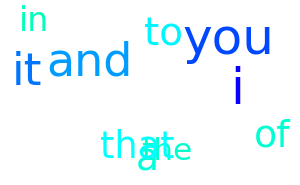
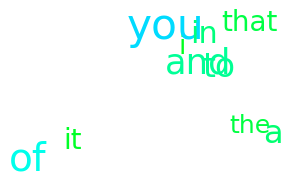
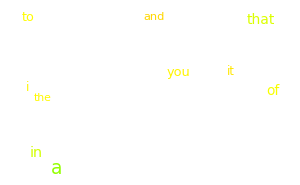
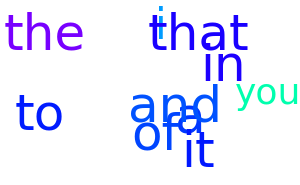
{-Graphics-Female → Female,-Graphics-Female → Male,-Graphics-Male → Female,-Graphics-Male → Male}

```mathematica
textPlane[top["Facebook",10],10]
```

```mathematica
list=Take[top["Facebook",50],{2,-1}];
```

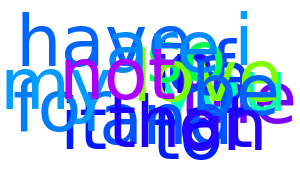
-Graphics-Male → Male

```mathematica
Panel[Labeled[Graphics[Table[Text[Style[list[[i,1]],Hue[1.75list[[i,5]]/Total[list[[i,2;;-1]]]],Italic,100(list[[i,5]]/99)],RandomReal[1,{2}],Automatic],{i,20}],AspectRatio->1/GoldenRatio,ImageSize->300],{"Male → Male"},{Top}]]
```

```mathematica
returnPi[string_,list_]:=Panel[PieChart[Take[#,{2,-1}],ChartLabels->Placed[{ToString[Round[100(#[[2]]/Total[Take[#,{2,-1}]])]]<>"%",ToString[Round[100(#[[3]]/Total[Take[#,{2,-1}]])]]<>"%",ToString[Round[100(#[[4]]/Total[Take[#,{2,-1}]])]]<>"%" ,ToString[Round[100(#[[5]]/Total[Take[#,{2,-1}]])]]<>"%"},"VerticalCallout"],PlotLabel->Panel[Text[Style[#[[1]],Bold]],FrameMargins->0],Ticks-> None,ChartLegends->legend[#],LegendAppearance->{LegendLabel-> Panel["Comment Gender → Status Gender",FrameMargins->0]}],FrameMargins->0]&/@Join[Delete[Table[Select[list,MatchQ[#,{i,_,_,_,_}]&],{i,Transpose[wordCount[string]][[1]]}],0]]
```

```mathematica
Transpose[wordCount["I like to eat pi pi to"]]
```

{{eat,i,like,pi,to},{1,1,1,2,2}}

```mathematica
string="Hello, I like to eat pie and what am I doing"
```

Hello, I like to eat pie and what am I doing

```mathematica
returnPi["words I am speaking words",Take[Import[notebookLocation<>"Facebook"<>"Database.csv"],{2,-1}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ClearSystemCache[]
```